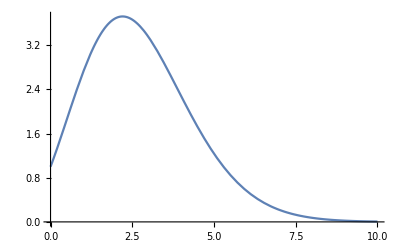

```mathematica
Plot[Exp[n]/n!,{n,0,10}]
```

```mathematica
D[a^n/n!,n]==0//FullSimplify
```

a^n (EulerGamma-HarmonicNumber[n]+Log[a])==0

```mathematica
D[HarmonicNumber[n],n]/.n->0
```

π^2/6

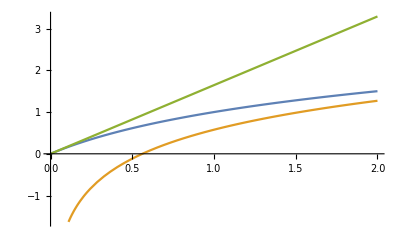

```mathematica
Plot[{HarmonicNumber[n],Log[n]+EulerGamma,Pi^2/6 n},{n,0,2}]
```

```mathematica
EulerGamma//N
```

0.577216

```mathematica
EulerGamma 6/Pi^2//N
```

0.350905

```mathematica
Solve[a^n (EulerGamma-HarmonicNumber[n]+Log[a])==0,n]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[a^n (EulerGamma-HarmonicNumber[n]+Log[a])==0,n]

```mathematica
partscore[p_]:=Times@@((#[[1]]!)^#[[2]] #[[2]]! &/@ Tally[p])
```

```mathematica
?SortBy
```

```mathematica
SortBy[IntegerPartitions[10],partscore][[1]]
```

{4,3,2,1}

```mathematica
partscore/@IntegerPartitions[5]
```

{120,24,12,12,8,12,120}

```mathematica
Tally[{2,2,2,1,1,1,1}]
```

{{2,3},{1,4}}

```mathematica
myparts=SortBy[IntegerPartitions[#],partscore][[1]]&/@Range[41]
```

{{1},{2},{2,1},{2,1,1},{2,2,1},{3,2,1},{3,2,1,1},{3,2,2,1},{3,2,2,1,1},{4,3,2,1},{3,3,2,2,1},{4,3,2,2,1},{4,3,2,2,1,1},{4,3,2,2,2,1},{4,3,3,2,2,1},{4,3,3,2,2,1,1},{4,3,3,2,2,2,1},{4,3,3,2,2,2,1,1},{4,3,3,3,2,2,1,1},{4,4,3,3,2,2,1,1},{4,3,3,3,2,2,2,1,1},{4,4,3,3,2,2,2,1,1},{5,4,3,3,2,2,2,1,1},{5,4,3,3,3,2,2,1,1},{4,4,3,3,3,2,2,2,1,1},{5,4,3,3,3,2,2,2,1,1},{5,4,4,3,3,2,2,2,1,1},{5,4,4,3,3,3,2,2,1,1},{5,4,4,3,3,2,2,2,2,1,1},{5,4,4,3,3,3,2,2,2,1,1},{5,4,4,3,3,3,2,2,2,1,1,1},{5,4,4,3,3,3,2,2,2,2,1,1},{5,4,4,3,3,3,3,2,2,2,1,1},{5,4,4,4,3,3,3,2,2,2,1,1},{5,4,4,3,3,3,3,2,2,2,2,1,1},{5,4,4,4,3,3,3,2,2,2,2,1,1},{5,4,4,4,3,3,3,3,2,2,2,1,1},{5,4,4,4,3,3,3,3,2,2,2,1,1,1},{5,4,4,4,3,3,3,3,2,2,2,2,1,1},{5,4,4,4,3,3,3,3,2,2,2,2,1,1,1},{5,5,4,4,4,3,3,3,2,2,2,2,1,1}}

```mathematica
Transpose[{Range[41],Reverse[#[[2]]&/@Tally[#]]&/@myparts}]
```

{{1,{1}},{2,{1}},{3,{1,1}},{4,{2,1}},{5,{1,2}},{6,{1,1,1}},{7,{2,1,1}},{8,{1,2,1}},{9,{2,2,1}},{10,{1,1,1,1}},{11,{1,2,2}},{12,{1,2,1,1}},{13,{2,2,1,1}},{14,{1,3,1,1}},{15,{1,2,2,1}},{16,{2,2,2,1}},{17,{1,3,2,1}},{18,{2,3,2,1}},{19,{2,2,3,1}},{20,{2,2,2,2}},{21,{2,3,3,1}},{22,{2,3,2,2}},{23,{2,3,2,1,1}},{24,{2,2,3,1,1}},{25,{2,3,3,2}},{26,{2,3,3,1,1}},{27,{2,3,2,2,1}},{28,{2,2,3,2,1}},{29,{2,4,2,2,1}},{30,{2,3,3,2,1}},{31,{3,3,3,2,1}},{32,{2,4,3,2,1}},{33,{2,3,4,2,1}},{34,{2,3,3,3,1}},{35,{2,4,4,2,1}},{36,{2,4,3,3,1}},{37,{2,3,4,3,1}},{38,{3,3,4,3,1}},{39,{2,4,4,3,1}},{40,{3,4,4,3,1}},{41,{2,4,3,3,2}}}

```mathematica
SortBy[IntegerPartitions[50],partscore][[1]]
```

{6,5,5,4,4,4,3,3,3,3,2,2,2,2,1,1}

```mathematica
SortBy[IntegerPartitions[60],partscore][[1]]
```

{6,5,5,4,4,4,4,3,3,3,3,3,2,2,2,2,2,1,1,1}

```mathematica
Tally[SortBy[IntegerPartitions[#],partscore][[1]]]&/@Range[50,60]
```

{{{6,1},{5,2},{4,3},{3,4},{2,4},{1,2}},{{6,1},{5,2},{4,3},{3,4},{2,4},{1,3}},{{6,1},{5,2},{4,3},{3,4},{2,5},{1,2}},{{6,1},{5,2},{4,3},{3,5},{2,4},{1,2}},{{6,1},{5,2},{4,3},{3,5},{2,4},{1,3}},{{6,1},{5,2},{4,4},{3,4},{2,4},{1,3}},{{6,1},{5,2},{4,3},{3,5},{2,5},{1,3}},{{6,1},{5,2},{4,4},{3,5},{2,4},{1,2}},{{6,1},{5,2},{4,4},{3,5},{2,4},{1,3}},{{6,1},{5,2},{4,4},{3,5},{2,5},{1,2}},{{6,1},{5,2},{4,4},{3,5},{2,5},{1,3}}}

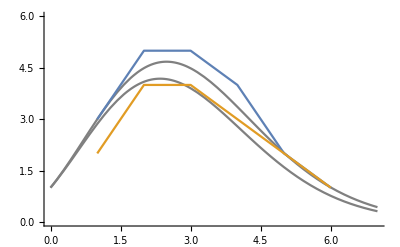

```mathematica
Show[Plot[{ProductLog[60]^n/n!,ProductLog[50]^n/n!},{n,0,7},PlotStyle->Gray,PlotRange->{All,{0,6}}],ListPlot[{Tally[%36],Tally[%33]},Joined->True]]
```

```mathematica
Exp[x]/(Exp[x]+Exp[-x])//FullSimplify
```

1/2 (1+Tanh[x])

```mathematica
softceil[x_]:=Sum[1/2 (1+Tanh[20(x-n)]),{n,0,100}]
```

```mathematica
softceil[3.]
```

3.5

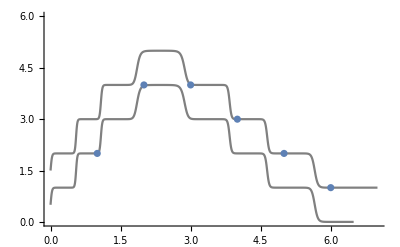

```mathematica
Show[Plot[{softceil[ProductLog[50]^n/n!],softceil[ProductLog[50]^n/n!]-1},{n,0,7},PlotStyle->Gray,PlotRange->{All,{0,6}}],ListPlot[{Tally[%33]},Joined->False]]
```

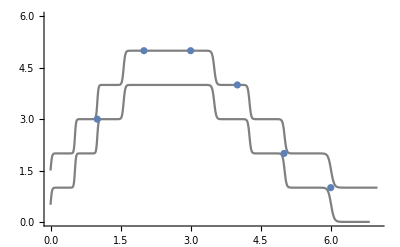

```mathematica
Show[Plot[{softceil[ProductLog[60]^n/n!],softceil[ProductLog[60]^n/n!]-1},{n,0,7},PlotStyle->Gray,PlotRange->{All,{0,6}}],ListPlot[{Tally[%36]},Joined->False]]
```

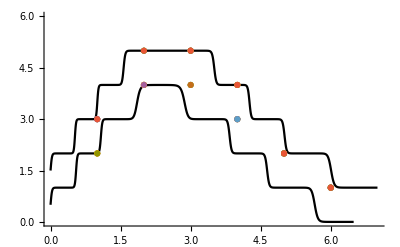

```mathematica
Show[Plot[{softceil[ProductLog[60]^n/n!],softceil[ProductLog[50]^n/n!]-1},{n,0,7},PlotStyle->Black,PlotRange->{All,{0,6}}],ListPlot[%79,Joined->False]]
```

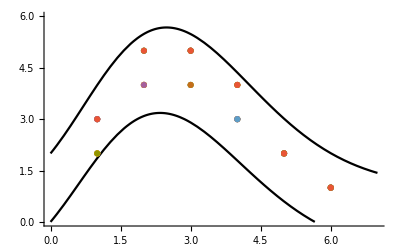

```mathematica
Show[Plot[{1+ProductLog[60]^n/n!,ProductLog[50]^n/n!-1},{n,0,7},PlotStyle->Black,PlotRange->{All,{0,6}}],ListPlot[%79,Joined->False]]
```

```mathematica
Sum[a^n/(n-1)!,{n,1,Infinity}]
```

a ⅇ^a

```mathematica
ProductLog[60]//N
```

2.9968

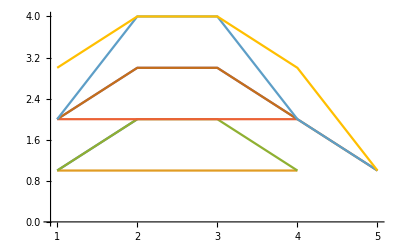

```mathematica
ListPlot[Tally/@myparts[[5;;;;5]],Joined->True]
```

```mathematica
IntegerPartitions[50]//Length
```

204226

```mathematica
PartitionsP[50]
```

204226

```mathematica
2000/8
```

250

```mathematica
Sum[Log[(3^n/(n!))!]+(3^n/(n!))Log[n!],{n,1,Infinity}]//N
```

57.2115

```mathematica
Sum[Log[(a^n/(n!))!],{n,1,Infinity}]
```

```mathematica
Sum[(a^n/(n!))Log[n!],{n,1,Infinity}]
```